```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{S[1]}->{}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={S[1]}->{};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 0];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 17 Particles insertions

Restoring 24 field point(s)

in total: 17 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 17 Particles amplitudes

in total: 17 Particles amplitudes

> Top. 1 ab/0/bb.m, 0 diagrams

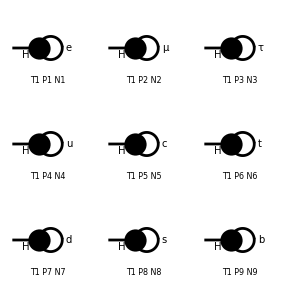

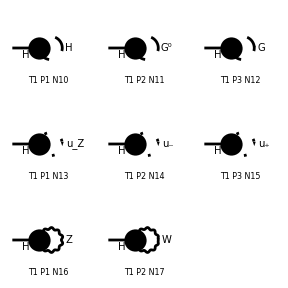

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L];
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/feynArts_amplitudes/OneLoopAmplitudes.m

```mathematica
FullForm[myAmp1L[[5]]]
```

Times[Rational[-1,16],Power[Pi,-4],FeynAmpDenominator[PropagatorDenominator[FourMomentum[Internal,1],MC]],MatrixTrace[NonCommutative[Plus[MC,DiracSlash[Times[-1,FourMomentum[Internal,1]]]]],Plus[Times[Complex[0,1],EL,gHuu,MC,NonCommutative[ChiralityProjector[-1]]],Times[Complex[0,1],EL,gHuu,MC,NonCommutative[ChiralityProjector[1]]]]],SumOver[Index[Colour,2],3]]

## Interference

```mathematica
myAmp1L[[1]]
```

-(FeynAmpDenominator[1/(-ME^2+(q1)^2)] tr[ME+gs[-(q1)],ⅈ EL gHll ME om_-+ⅈ EL gHll ME om_+])/(16 π^4)

```mathematica
SquareSimplifyAndSave[myAmp1L,{1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_14_1.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_15_1.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_16_1.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH//interferences/Contribution_17_1.m.

## Shift

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,17},{j,1}]
```

ABISS: Integral family {{B0, {ME}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_1_1.m.

ABISS: Integral family {{B0, {mm}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_2_1.m.

ABISS: Integral family {{B0, {ML}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_3_1.m.

ABISS: Integral family {{B0, {mu}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_4_1.m.

ABISS: Integral family {{B0, {MC}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_5_1.m.

ABISS: Integral family {{B0, {MT}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_6_1.m.

ABISS: Integral family {{B0, {md}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_7_1.m.

ABISS: Integral family {{B0, {MS}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_8_1.m.

ABISS: Integral family {{B0, {MB}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_9_1.m.

ABISS: Integral family {{B0, {MH}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_10_1.m.

ABISS: Integral family {{B0, {mz}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_11_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_12_1.m.

ABISS: Integral family {{B0, {mz}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_13_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_14_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_15_1.m.

ABISS: Integral family {{B0, {mz}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_16_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/interferences/Contribution_17_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,17},{j,1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_14_1.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_15_1.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_16_1.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/TH/kira_input/Contribution_17_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[B0,{ME},1],userIntegral[B0,{mm},1],userIntegral[B0,{ML},1],userIntegral[B0,{mu},1],userIntegral[B0,{MC},1],userIntegral[B0,{MT},1],userIntegral[B0,{md},1],userIntegral[B0,{MS},1],userIntegral[B0,{MB},1],userIntegral[B0,{MH},1],userIntegral[B0,{mz},1],userIntegral[B0,{mw},1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
PrintRules[]
```

{}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[B0,{ME},1],userIntegral[B0,{mm},1],userIntegral[B0,{ML},1],userIntegral[B0,{mu},1],userIntegral[B0,{MC},1],userIntegral[B0,{MT},1],userIntegral[B0,{md},1],userIntegral[B0,{MS},1],userIntegral[B0,{MB},1],userIntegral[B0,{MH},1],userIntegral[B0,{mz},1],userIntegral[B0,{mw},1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{ME},1],userIntegral[B0,{mm},1],userIntegral[B0,{ML},1],userIntegral[B0,{mu},1],userIntegral[B0,{MC},1],userIntegral[B0,{MT},1],userIntegral[B0,{md},1],userIntegral[B0,{MS},1],userIntegral[B0,{MB},1],userIntegral[B0,{MH},1],userIntegral[B0,{mz},1],userIntegral[B0,{mw},1]}

```mathematica
Do[
SaveResult[i,j];
,{i,17},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,17}]
```

```mathematica
diagramCoefficients
```

{{-(ⅈ EL gHll ME^2)/(4 π^4),0,0,0,0,0,0,0,0,0,0,0},{0,-(ⅈ EL gHll mm^2)/(4 π^4),0,0,0,0,0,0,0,0,0,0},{0,0,-(ⅈ EL gHll ML^2)/(4 π^4),0,0,0,0,0,0,0,0,0},{0,0,0,-(3 ⅈ EL gHuu mu^2)/(4 π^4),0,0,0,0,0,0,0,0},{0,0,0,0,-(3 ⅈ EL gHuu MC^2)/(4 π^4),0,0,0,0,0,0,0},{0,0,0,0,0,-(3 ⅈ EL gHuu MT^2)/(4 π^4),0,0,0,0,0,0},{0,0,0,0,0,0,-(3 ⅈ EL gHdd md^2)/(4 π^4),0,0,0,0,0},{0,0,0,0,0,0,0,-(3 ⅈ EL gHdd MS^2)/(4 π^4),0,0,0,0},{0,0,0,0,0,0,0,0,-(3 ⅈ EL gHdd MB^2)/(4 π^4),0,0,0},{0,0,0,0,0,0,0,0,0,(ⅈ EL gHHH MH^2)/(32 π^4),0,0},{0,0,0,0,0,0,0,0,0,0,(ⅈ EL gHXX MH^2)/(32 π^4),0},{0,0,0,0,0,0,0,0,0,0,0,(ⅈ EL gHFF MH^2)/(16 π^4)},{0,0,0,0,0,0,0,0,0,0,-(ⅈ EL gHgzgz)/(32 π^4),0},{0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL gHgmgm)/(32 π^4)},{0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL gHgpgp)/(32 π^4)},{0,0,0,0,0,0,0,0,0,0,-(ⅈ d EL gHZZ)/(32 π^4),0},{0,0,0,0,0,0,0,0,0,0,0,-(ⅈ d EL gHWW)/(16 π^4)}}

```mathematica
coefficients=Plus@@diagramCoefficients
```

{-(ⅈ EL gHll ME^2)/(4 π^4),-(ⅈ EL gHll mm^2)/(4 π^4),-(ⅈ EL gHll ML^2)/(4 π^4),-(3 ⅈ EL gHuu mu^2)/(4 π^4),-(3 ⅈ EL gHuu MC^2)/(4 π^4),-(3 ⅈ EL gHuu MT^2)/(4 π^4),-(3 ⅈ EL gHdd md^2)/(4 π^4),-(3 ⅈ EL gHdd MS^2)/(4 π^4),-(3 ⅈ EL gHdd MB^2)/(4 π^4),(ⅈ EL gHHH MH^2)/(32 π^4),-(ⅈ EL gHgzgz)/(32 π^4)-(ⅈ d EL gHZZ)/(32 π^4)+(ⅈ EL gHXX MH^2)/(32 π^4),-(ⅈ EL gHgmgm)/(32 π^4)-(ⅈ EL gHgpgp)/(32 π^4)-(ⅈ d EL gHWW)/(16 π^4)+(ⅈ EL gHFF MH^2)/(16 π^4)}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
parameterReplace=smparameters
```

{gZlL→(-1/2+SW^2)/(CW SW),gZlR→SW/CW,gZNL→1/(2 CW SW),gZuL→(1/2-(2 SW^2)/3)/(CW SW),gZuR→-(2 SW)/(3 CW),gZdL→(-1/2+SW^2/3)/(CW SW),gZdR→SW/(3 CW),gAl→1,gAu→-2/3,gAd→1/3,gWNl→1/(√2 SW),gWlN→1/(√2 SW),gWud→1/(√2 SW),gWdu→1/(√2 SW),gWWZ→CW/SW,gWWA→1,gWWWW→1/SW^2,gWWZZ→-CW^2/SW^2,gWWAZ→CW/SW,gWWAA→-1,gHHHH→-3/(4 MW^2 SW^2),gXXXX→-3/(4 MW^2 SW^2),gHHXX→1/(2 SW^2),gHHFF→1/(2 SW^2),gXXFF→1/(2 SW^2),gFFFF→1/(2 SW^2),gHXFF→1/(4 CW^2),gHHH→-3/(2 MW SW),gHXX→-1/(2 MW SW),gHFF→-1/(2 MW SW),gXFF→(MW SW)/(2 CW^2),gHHZZ→1/(2 CW^2 SW^2),gXXZZ→1/(2 CW^2 SW^2),gHHWW→1/(2 SW^2),gXXWW→1/(2 SW^2),gFFWW→1/(2 SW^2),gFFAA→2,gFFAZ→(-CW^2+SW^2)/(CW SW),gFFZZ→((-CW^2+SW^2)^2)/(2 CW^2 SW^2),gHFAW→-1/(2 SW),gHFZW→-1/(2 CW),gXFAW→1/(2 SW),gHFZW→-1/(2 CW),gXFZW→1/(2 CW),gHXWW→1/(2 SW^2),gHXZ→1/(2 CW SW),gFFA→1,gFFZ→(CW^2-SW^2)/(2 CW SW),gHFW→1/(2 SW),gXFW→1/(2 SW),gHZZ→MW/(CW^2 SW),gHWW→MW/SW,gXWW→MW/SW,gFAW→-MW,gFZW→MW/CW,gHll→-1/(2 MW SW),gHuu→-1/(2 MW SW),gHdd→-1/(2 MW SW),gXll→1/(2 MW SW),gXuu→1/(2 MW SW),gXdd→1/(2 MW SW),gFll→1/(√2 MW SW),gFud→1/(√2 MW SW),gFdu→1/(√2 MW SW),ggpgpA→1,ggmgmA→1,ggpgpZ→CW/SW,ggmgmZ→CW/SW,ggzgpW→CW/SW,ggzgmW→CW/SW,ggagpW→1,ggagmW→1,gHgzgz→-MW/(CW^2 SW),gHgpgp→-MW/SW,gHgmgm→-MW/SW,gXgpgp→MW/(2 SW),gXgmgm→MW/(2 SW),gFgzgp→MW/CW,gFgzgm→MW/CW,gFgagm→MW,gFgagp→MW,ggpgpAA→1,ggmgmAA→1,ggpgpAZ→-CW/SW,ggmgmAZ→-CW/SW,ggpgpZZ→CW^2/SW^2,ggmgmZZ→CW^2/SW^2,ggagpAW→-1,ggagmAW→-1,ggagpZW→CW/SW,ggagmZW→CW/SW,ggzgpAW→CW/SW,ggzgmAW→CW/SW,ggzgpZW→-CW^2/SW^2,ggzgmZW→-CW^2/SW^2,ggagaWW→1,ggagzWW→-CW/SW,ggzgzWW→CW^2/SW^2,ggpgpWW→1/SW^2,ggmgmWW→1/SW^2,ggpgmWW→-1/SW^2,gHHgzgz→-1/(2 CW^2 SW^2),gHHgpgp→-1/(2 SW^2),gHHgmgm→-1/(2 SW^2),gXXgzgz→-1/(2 CW^2 SW^2),gXXgpgp→-1/(2 SW^2),gXXgmgm→-1/(2 SW^2),gFFgaga→-1,gFFgzgz→((CW^2-SW^2)^2)/(2 CW^2 SW^2),gFFgpgp→-1/(2 SW^2),gFFgmgm→-1/(2 SW^2),gFFgagz→(CW^2-SW^2)/(CW SW),gHXgpgp→1/(4 SW^2),gHXgmgm→1/(4 SW^2),gHFgagp→1/(2 SW),gHFgagm→1/(2 SW),gHFgzgp→1/(2 CW),gHFgzgm→1/(2 CW),gXFgagp→1/(2 SW),gXFgagm→1/(2 SW),gXFgzgp→1/(2 CW),gXFgzgm→1/(2 CW)}

```mathematica
out=-I coefficients/.parameterReplace//Simplify
```

{(EL ME^2)/(8 MW π^4 SW),(EL mm^2)/(8 MW π^4 SW),(EL ML^2)/(8 MW π^4 SW),(3 EL mu^2)/(8 MW π^4 SW),(3 EL MC^2)/(8 MW π^4 SW),(3 EL MT^2)/(8 MW π^4 SW),(3 EL md^2)/(8 MW π^4 SW),(3 EL MS^2)/(8 MW π^4 SW),(3 EL MB^2)/(8 MW π^4 SW),-(3 EL MH^2)/(64 MW π^4 SW),-(EL (CW^2 MH^2+2 (-1+d) MW^2))/(64 CW^2 MW π^4 SW),-(EL (MH^2+2 (-1+d) MW^2))/(32 MW π^4 SW)}

```mathematica
out>>(NotebookDirectory[]<>"result.m")
```